# EINSTEIN ENERGY MOMENTUM PSEUDOPSEUDOTENSOR

## SCHWARZSCHILD IN HARMONIC COORDINATES

November 2021

This notebook is supplementary material for the paper
Weiss variation for general boundaries
by Sumanta Chakraborty and Justin C. Feng

This notebook was written in Mathematica 12. The conventions should be consistent with Spacetime and Geometry: An Introduction to General Relativity by Sean Carroll.

## GENERAL FUNCTIONS

### METRIC FUNCTIONS

This function computes the metric product

```mathematica
met[g_,V1_,V2_]:=Module[{W},
W=g.V2;
V1.W]
```

### RANK 2 SYMMETRIZER

This function symmetrizes a rank-2 tensor:

```mathematica
Symrcalc[T_,n_]:=Module[{},
Table[(T[[ii,ji]]+T[[ji,ii]])/2,{ii,1,n},{ji,1,n}]];
```

### CONNECTION COEFFICIENTS

This function calculates the connection coefficients:

```mathematica
Gamcalc[g_,X_,n_]:=Module[{Gam,gin},
gin=Inverse[g];
Gam=Table[(1/2)*Sum[gin[[ki,li]]*(D[g[[li,bi]],X[[ai]]]+D[g[[ai,li]],X[[bi]]]-D[g[[ai,bi]],X[[li]]]),{li,1,n}],{ki,1,n},{ai,1,n},{bi,1,n}];
Gam];
```

### LEVI-CIVITA AND GENERALIZED KRONECKERS

These functions compute the raised and lowered index Levi-Civita pseudotensors:

```mathematica
(* LOWERED INDICES *)
epsLcalc[g_,X_,n_,s_]:=Module[{vol},
vol=Sqrt[s*Det[g]];
vol*LeviCivitaTensor[n]];

(* RAISED INDICES *)
epsRcalc[g_,X_,n_,s_]:=Module[{gin,epsL},
gin=Inverse[g];
epsL=epsLcalc[g,X,n,s];
Table[Sum[gin[[ii,ai]]*gin[[ji,bi]]*gin[[ki,ci]]*gin[[li,di]]*epsL[[ai,bi,ci,di]],{ai,1,n},{bi,1,n},{ci,1,n},{di,1,n}],{ii,1,n},{ji,1,n},{ki,1,n},{li,1,n}]];
```

This function computes the generalized Kronecker delta at the top level (the rest can be constructed using TensorContract):

```mathematica
(* LOWERED INDICES *)
gkdcalcn[n_]:=Module[{δ,M},
TensorProduct[LeviCivitaTensor[n],LeviCivitaTensor[n]]
];
```

### COVARIANT DERIVATIVE CALCULATORS

#### LOWERED INDEX VECTOR

This function calculates the covariant derivative of a lowered index vector:

```mathematica
CDVLcalc[V_,g_,X_,n_]:=Module[{Gam},
Gam=Gamcalc[g,X,n];
Table[D[V[[ai]],X[[bi]]]-Sum[Gam[[si,bi,ai]]V[[si]],{si,1,n}],{ai,1,n},{bi,1,n}]];
```

#### RAISED INDEX VECTOR

This function calculates the covariant derivative of a raised index vector:

```mathematica
CDVRcalc[V_,g_,X_,n_]:=Module[{Gam},
Gam=Gamcalc[g,X,n];
Table[D[V[[ai]],X[[bi]]]+Sum[Gam[[ai,bi,si]]V[[si]],{si,1,n}],{ai,1,n},{bi,1,n}]];
```

#### LOWERED INDEX VECTOR (GENERAL CONNECTION)

This function calculates the covariant derivative of a lowered index vector:

```mathematica
CDGVLcalc[V_,Gam_,X_,n_]:=Module[{},
Table[D[V[[ai]],X[[bi]]]-Sum[Gam[[si,bi,ai]]V[[si]],{si,1,n}],{ai,1,n},{bi,1,n}]];
```

#### RAISED INDEX VECTOR (GENERAL CONNECTION)

This function calculates the covariant derivative of a raised index vector:

```mathematica
CDGVRcalc[V_,Gam_,X_,n_]:=Module[{},
Table[D[V[[ai]],X[[bi]]]+Sum[Gam[[ai,bi,si]]V[[si]],{si,1,n}],{ai,1,n},{bi,1,n}]];
```

#### MIXED INDEX RANK-2 TENSOR (GENERAL CONNECTION)

This function calculates the covariant derivative of a mixed index tensor (first index raised):

```mathematica
CDGT2Rcalc[T_,Gam_,X_,n_]:=Module[{},
Table[D[T[[ai,bi]],X[[ci]]]+Sum[Gam[[ai,ci,si]]T[[si,bi]]-Gam[[si,ci,bi]]T[[ai,si]],{si,1,n}],{ai,1,n},{bi,1,n},{ci,1,n}]];
```

### TORSION CALCULATOR

```mathematica
Torsioncalc[Gam_,X_,n_]:=Module[{},
Table[Gam[[ii,ai,bi]]-Gam[[ii,bi,ai]],{ii,1,n},{ai,1,n},{bi,1,n}]];
```

### RIEMANN CALCULATOR

#### RIEMANN TENSOR

```mathematica
Riemanncalc[g_,X_,n_]:=Module[{Gam},
Gam=Gamcalc[g,X,n];
Table[D[Gam[[ii,bi,ji]],X[[ai]]]-D[Gam[[ii,ai,ji]],X[[bi]]]+Sum[Gam[[ii,ai,si]]*Gam[[si,bi,ji]]-Gam[[ii,bi,si]]*Gam[[si,ai,ji]],{si,1,n}],{ii,1,n},{ji,1,n},{ai,1,n},{bi,1,n}]];
```

```mathematica
(*  *)
RiemanncalcS[Gam_,X_,n_]:=Module[{},
Table[D[Gam[[ii,bi,ji]],X[[ai]]]-D[Gam[[ii,ai,ji]],X[[bi]]]+Sum[Gam[[ii,ai,si]]*Gam[[si,bi,ji]]-Gam[[ii,bi,si]]*Gam[[si,ai,ji]],{si,1,n}],{ii,1,n},{ji,1,n},{ai,1,n},{bi,1,n}]];
```

#### RIEMANN TENSOR IN ALL LOWERED INDICES

```mathematica
RiemannLcalc[g_,X_,n_]:=Module[{Riemann},
Riemann=Riemanncalc[g,X,n];
Table[Sum[g[[ii,si]]*Riemann[[si,ji,ai,bi]],{si,1,n}],{ii,1,n},{ji,1,n},{ai,1,n},{bi,1,n}]];
```

```mathematica
(*  *)
RiemannLcalcS[g_,Riemann_,X_,n_]:=Module[{},
Table[Sum[g[[ii,si]]*Riemann[[si,ji,ai,bi]],{si,1,n}],{ii,1,n},{ji,1,n},{ai,1,n},{bi,1,n}]];
```

#### RIEMANN TENSOR IN ALL RAISED INDICES

```mathematica
RiemannUcalc[g_,X_,n_]:=Module[{Riemann,gin},
Riemann=Riemanncalc[g,X,n];
gin=Inverse[g];
Table[Sum[gin[[ji,si]]*gin[[ai,mi]]*gin[[bi,ni]]*Riemann[[ii,si,mi,ni]],{si,1,n},{mi,1,n},{ni,1,n}],{ii,1,n},{ji,1,n},{ai,1,n},{bi,1,n}]];
```

```mathematica
(*  *)
RiemannUcalcS[g_,gin_,Riemann_,X_,n_]:=Module[{},
Table[Sum[gin[[ji,si]]*gin[[ai,mi]]*gin[[bi,ni]]*Riemann[[ii,si,mi,ni]],{si,1,n},{mi,1,n},{ni,1,n}],{ii,1,n},{ji,1,n},{ai,1,n},{bi,1,n}]];
```

#### RIEMANN TENSOR (FIRST TWO RAISED)

```mathematica
RiemannU1calc[g_,X_,n_]:=Module[{Riemann,gin},
Riemann=Riemanncalc[g,X,n];
gin=Inverse[g];
Table[Sum[gin[[ji,si]]*Riemann[[ii,si,ai,bi]],{si,1,n}],{ii,1,n},{ji,1,n},{ai,1,n},{bi,1,n}]];
```

```mathematica
(*  *)
RiemannU1calcS[g_,gin_,Riemann_,X_,n_]:=Module[{},
Table[Sum[gin[[ji,si]]*Riemann[[ii,si,ai,bi]],{si,1,n}],{ii,1,n},{ji,1,n},{ai,1,n},{bi,1,n}]];
```

#### RIEMANN TENSOR (SECOND TWO RAISED)

```mathematica
RiemannU2calc[g_,X_,n_]:=Module[{RiemannL,gin},
RiemannL=RiemannLcalc[g,X,n];
gin=Inverse[g];
Table[Sum[gin[[ai,mi]]*gin[[bi,ni]]*RiemannL[[ii,ji,mi,ni]],{mi,1,n},{ni,1,n}],{ii,1,n},{ji,1,n},{ai,1,n},{bi,1,n}]];
```

```mathematica
(*  *)
RiemannU2calcS[g_,gin_,RiemannL_,X_,n_]:=Module[{},
Table[Sum[gin[[ai,mi]]*gin[[bi,ni]]*RiemannL[[ii,ji,mi,ni]],{mi,1,n},{ni,1,n}],{ii,1,n},{ji,1,n},{ai,1,n},{bi,1,n}]];
```

### RICCI CALCULATOR

#### RICCI TENSOR

This function calculates the Ricci curvature in lowered indices:

```mathematica
RicciLcalc[g_,X_,n_]:=Module[{Gam},
Gam=Gamcalc[g,X,n];
Table[Sum[D[Gam[[ai,ii,ji]],X[[ai]]]-D[Gam[[ai,ai,ji]],X[[ii]]]+Sum[Gam[[ai,ai,si]]*Gam[[si,ii,ji]]-Gam[[ai,ii,si]]*Gam[[si,ai,ji]],{si,1,n}],{ai,1,n}],{ii,1,n},{ji,1,n}]];
```

#### RICCI SCALAR

This function calculates the Ricci scalar:

```mathematica
RicciScalc[g_,X_,n_]:=Module[{gin,Ricci},
gin=Inverse[g];
Ricci=RicciLcalc[g,X,n];
Sum[gin[[ii,ji]]Ricci[[ii,ji]],{ii,1,n},{ji,1,n}]];
```

#### EINSTEIN TENSOR

```mathematica
(* EINSTEIN TENSOR *)
EinsteinLcalc[g_,X_,n_]:=Module[{Ricci,R},
Ricci=RicciLcalc[g,X,n];
R=RicciScalc[g,X,n];
Table[(Ricci[[ai,bi]]-R/2 g[[ai,bi]]),{ai,1,n},{bi,1,n}]];
```

### WEYL TENSOR

#### SCHOUTEN TENSOR

```mathematica
Schoutencalc[g_,X_,n_]:=Module[{R,Ricci},
Ricci=RicciLcalc[g,X,n];
R=RicciScalc[g,X,n];
Table[1/(n-2)(R/(2*(n-1))g[[ai,bi]]-Ricci[[ai,bi]]),{ai,1,n},{bi,1,n}]];
```

```mathematica
(*  *)
SchoutencalcS[g_,R_,Ricci_,X_,n_]:=Module[{},
Table[1/(n-2)(R/(2*(n-1))g[[ai,bi]]-Ricci[[ai,bi]]),{ai,1,n},{bi,1,n}]];
```

#### WEYL TENSOR

```mathematica
WeylLcalc[g_,X_,n_]:=Module[{Schouten,RiemannL},
Schouten=Schoutencalc[g,X,n];
RiemannL=RiemannLcalc[g,X,n];
Table[(RiemannL[[ai,bi,ci,di]]-(g[[ai,di]]*Schouten[[ci,bi]]-g[[ai,ci]]*Schouten[[di,bi]])+(g[[bi,di]]*Schouten[[ci,ai]]-g[[bi,ci]]*Schouten[[di,ai]])),
{ai,1,n},{bi,1,n},{ci,1,n},{di,1,n}]];
```

```mathematica
(*  *)
WeylLcalcS[g_,Schouten_,RiemannL_,X_,n_]:=Module[{},
Table[(RiemannL[[ai,bi,ci,di]]-(g[[ai,di]]*Schouten[[ci,bi]]-g[[ai,ci]]*Schouten[[di,bi]])+(g[[bi,di]]*Schouten[[ci,ai]]-g[[bi,ci]]*Schouten[[di,ai]])),
{ai,1,n},{bi,1,n},{ci,1,n},{di,1,n}]];
```

### HODGE DUAL CURVATURE

#### RIEMANN TENSOR LEFT DUAL

```mathematica
RiemannLDcalc[g_,X_,n_,s_]:=Module[{RiemannU1,gin,epsL},
RiemannU1=RiemannU1calc[g,X,n];
gin=Inverse[g];
epsL=epsLcalc[g,X,n,s];
Table[Sum[(1/2)*epsL[[ii,ji,mi,ni]]*RiemannU1[[mi,ni,ai,bi]],{mi,1,n},{ni,1,n}],{ii,1,n},{ji,1,n},{ai,1,n},{bi,1,n}]];
```

```mathematica
(*  *)
RiemannLDcalcS[g_,gin_,epsL_,RiemannU1_,X_,n_,s_]:=Module[{},
Table[Sum[(1/2)*epsL[[ii,ji,mi,ni]]*RiemannU1[[mi,ni,ai,bi]],{mi,1,n},{ni,1,n}],{ii,1,n},{ji,1,n},{ai,1,n},{bi,1,n}]];
```

#### RIEMANN TENSOR RIGHT DUAL

```mathematica
RiemannRDcalc[g_,X_,n_,s_]:=Module[{RiemannU2,gin,epsL},
RiemannU2=RiemannU2calc[g,X,n];
gin=Inverse[g];
epsL=epsLcalc[g,X,n,s];
Table[Sum[(1/2)*RiemannU2[[ii,ji,mi,ni]]*epsL[[mi,ni,ai,bi]],{mi,1,n},{ni,1,n}],{ii,1,n},{ji,1,n},{ai,1,n},{bi,1,n}]];
```

```mathematica
(*  *)
RiemannRDcalcS[g_,gin_,epsL_,RiemannU2_,X_,n_,s_]:=Module[{},
Table[Sum[(1/2)*RiemannU2[[ii,ji,mi,ni]]*epsL[[mi,ni,ai,bi]],{mi,1,n},{ni,1,n}],{ii,1,n},{ji,1,n},{ai,1,n},{bi,1,n}]];
```

#### RIEMANN TENSOR DOUBLE DUAL

```mathematica
RiemannDDcalc[g_,X_,n_,s_]:=Module[{RiemannLD,gin,epsL},
RiemannLD=RiemannLDcalc[g,X,n,s];
gin=Inverse[g];
epsL=epsLcalc[g,X,n,s];
Table[Sum[(1/2)*RiemannLD[[ii,ji,mi,ni]]*epsL[[mi,ni,ai,bi]],{mi,1,n},{ni,1,n}],{ii,1,n},{ji,1,n},{ai,1,n},{bi,1,n}]];
```

```mathematica
(*  *)
RiemannDDcalcS[g_,gin_,epsL_,RiemannLD_,X_,n_,s_]:=Module[{},
Table[Sum[(1/2)*RiemannLD[[ii,ji,mi,ni]]*epsL[[mi,ni,ai,bi]],{mi,1,n},{ni,1,n}],{ii,1,n},{ji,1,n},{ai,1,n},{bi,1,n}]];
```

### CURVATURE INVARIANTS

#### RICCI SQUARED

```mathematica
RicciSq[g_,X_,n_]:=Module[{Ricci,gin},
Ricci=RicciLcalc[g,X,n];
gin=Inverse[g];
Sum[gin[[ci,ai]]*gin[[di,bi]]*Ricci[[ci,di]]*Ricci[[ai,bi]],{ai,1,n},{bi,1,n},{ci,1,n},{di,1,n}]];
```

```mathematica
RicciSqS[gin_,Ricci_,X_,n_]:=Module[{},
Sum[gin[[ci,ai]]*gin[[di,bi]]*Ricci[[ci,di]]*Ricci[[ai,bi]],{ai,1,n},{bi,1,n},{ci,1,n},{di,1,n}]];
```

#### KRETSCHMANN

```mathematica
Kretschmanncalc[g_,X_,n_]:=Module[{RiemannL,gin},
RiemannL=RiemannLcalc[g,X,n];
gin=Inverse[g];
Sum[gin[[i1,s1]]*gin[[i2,s2]]*gin[[i3,s3]]*gin[[i4,s4]]*RiemannL[[s1,s2,s3,s4]] *RiemannL[[i1,i2,i3,i4]] ,{s1,1,n},{s2,1,n},{s3,1,n},{s4,1,n},{i1,1,n},{i2,1,n},{i3,1,n},{i4,1,n}]];
```

```mathematica
KretschmanncalcS[gin_,RiemannL_,X_,n_]:=Module[{},
Sum[gin[[i1,s1]]*gin[[i2,s2]]*gin[[i3,s3]]*gin[[i4,s4]]*RiemannL[[s1,s2,s3,s4]] *RiemannL[[i1,i2,i3,i4]] ,{s1,1,n},{s2,1,n},{s3,1,n},{s4,1,n},{i1,1,n},{i2,1,n},{i3,1,n},{i4,1,n}]];
```

#### WEYL SQUARED

```mathematica
WeylSqcalc[g_,X_,n_]:=Module[{Weyl,gin},
Weyl=WeylLcalc[g,X,n];
gin=Inverse[g];
Sum[gin[[i1,s1]]*gin[[i2,s2]]*gin[[i3,s3]]*gin[[i4,s4]]*Weyl[[s1,s2,s3,s4]] *Weyl[[i1,i2,i3,i4]] ,{s1,1,n},{s2,1,n},{s3,1,n},{s4,1,n},{i1,1,n},{i2,1,n},{i3,1,n},{i4,1,n}]];
```

```mathematica
WeylSqcalcS[gin_,Weyl_,X_,n_]:=Module[{},
Sum[gin[[i1,s1]]*gin[[i2,s2]]*gin[[i3,s3]]*gin[[i4,s4]]*Weyl[[s1,s2,s3,s4]] *Weyl[[i1,i2,i3,i4]] ,{s1,1,n},{s2,1,n},{s3,1,n},{s4,1,n},{i1,1,n},{i2,1,n},{i3,1,n},{i4,1,n}]];
```

#### GAUSS-BONNET

```mathematica
GaBocalc[g_,X_,n_]:=Module[{R,RicciSquared,KretschRiem},
KretschRiem=Kretschmanncalc[g,X,n];
RicciSquared=RicciSq[g,X,n];
R=RicciScalc[g,X,n];
R^2-4RicciSquared+KretschRiem];
```

```mathematica
GaBocalcS[R_,RicciSquared_,KretschRiem_,X_,n_]:=Module[{},
R^2-4RicciSquared+KretschRiem];
```

#### CHERN-PONTRYAGIN

```mathematica
ChPocalc[g_,X_,n_,s_]:=Module[{RiemannL,RiemannLD,gin},
RiemannL=RiemannLcalc[g,X,n];
RiemannLD=RiemannLDcalc[g,X,n,s];
gin=Inverse[g];
Sum[gin[[i1,s1]]*gin[[i2,s2]]*gin[[i3,s3]]*gin[[i4,s4]]*RiemannLD[[s1,s2,s3,s4]] *RiemannL[[i1,i2,i3,i4]] ,{s1,1,n},{s2,1,n},{s3,1,n},{s4,1,n},{i1,1,n},{i2,1,n},{i3,1,n},{i4,1,n}]];
```

```mathematica
ChPocalcS[gin_,RiemannL_,RiemannLD_,X_,n_,s_]:=Module[{},
Sum[gin[[i1,s1]]*gin[[i2,s2]]*gin[[i3,s3]]*gin[[i4,s4]]*RiemannLD[[s1,s2,s3,s4]] *RiemannL[[i1,i2,i3,i4]] ,{s1,1,n},{s2,1,n},{s3,1,n},{s4,1,n},{i1,1,n},{i2,1,n},{i3,1,n},{i4,1,n}]];
```

#### EULER

```mathematica
Eulrcalc[g_,X_,n_,s_]:=Module[{RiemannL,RiemannDD,gin},
RiemannL=RiemannLcalc[g,X,n];
RiemannDD=RiemannDDcalc[g,X,n,s];
gin=Inverse[g];
Sum[gin[[i1,s1]]*gin[[i2,s2]]*gin[[i3,s3]]*gin[[i4,s4]]*RiemannDD[[s1,s2,s3,s4]] *RiemannL[[i1,i2,i3,i4]] ,{s1,1,n},{s2,1,n},{s3,1,n},{s4,1,n},{i1,1,n},{i2,1,n},{i3,1,n},{i4,1,n}]];
```

```mathematica
EulrcalcS[gin_,RiemannL_,RiemannDD_,X_,n_,s_]:=Module[{},
Sum[gin[[i1,s1]]*gin[[i2,s2]]*gin[[i3,s3]]*gin[[i4,s4]]*RiemannDD[[s1,s2,s3,s4]] *RiemannL[[i1,i2,i3,i4]] ,{s1,1,n},{s2,1,n},{s3,1,n},{s4,1,n},{i1,1,n},{i2,1,n},{i3,1,n},{i4,1,n}]];
```

### HYPERSURFACE STUFF

#### PROJECTION TENSOR

This function computes the projection tensor for non-null vectors V^μ:

(P^μ)_ν :=(δ^μ)_ν-V^μ V_ν/g (V,V)

```mathematica
proj[g_,V_,n_]:=Module[{gin,gV,VL,pTL},
gin=Inverse[g];
gv=met[g,V,V];
VL=g.V;
pTL=Table[g[[ii,ji]]-VL[[ii]]VL[[ji]]/gv,{ii,1,n},{ji,1,n}];
gin.pTL]
```

#### EXTRINSIC

We have two versions of the extrinsic curvature calculator so that they can provide independent checks.

##### VERSION A

The following calculates the Extrinsic curvature for a surface of constant coordinate s, according to the following formula:

K_ij =e_i^μ e_j^ν∇_μ n_ν

where the projection operators e_i^μ are defined in the following way (y^i being coordinates on the surface of constant coordinate s):

e_i^μ=(∂x^μ)/(∂y^i)

```mathematica
ExtrinsicLcalcA[s_,σ_,gb_,Xb_,Xs_,n_]:=Module[{gbin,CDN,e,NL,N1,nf},
gbin=Inverse[gb];
e=Table[D[Xb[[ii]],Xs[[ji]]],{ii,1,n},{ji,1,n-1}];
NL=Table[D[s,Xb[[ii]]],{ii,1,n}];
nf=σ/√(σ Sum[NL[[ii]]*NL[[ji]]*gbin[[ii,ji]],{ii,1,n},{ji,1,n}]);
N1=nf*NL;
CDN=CDVLcalc[N1,gb,Xb,n];
Table[Sum[e[[ai,ii]]e[[bi,ji]]CDN[[ai,bi]],{ai,1,n},{bi,1,n}],{ii,1,n-1},{ji,1,n-1}]]
```

##### VERSION B

The following calculates the Extrinsic curvature for a surface of constant coordinate s, given the lapse α and shift β_i, according to the following formula:

K_ij:=1/(2 α)(∂γ_ij)/(∂s)-2 D_((i)β_(j))

```mathematica
ExtrinsicLcalcB[s_,gs_,α_,β_,Xs_,n_]:=Module[{gsin,dtg,SSD,ExtrinsicL},
gsin=Inverse[gs];
dtg=Table[D[gs[[ii,ji]],s],{ii,1,n},{ji,1,n}];
SSD=2Symrcalc[CDVLcalc[β,gs,Xs,n],n];
(dtg-SSD)/(2α)];
```

### GHG CALCULATORS

These functions recalculate the Ricci tensor in the Generalized Harmonic Gauge (GHG)

#### GAUGE SOURCE FUNCTION

This function computes the Gauge source reference function

```mathematica
GaugeSourceRef[g_,X_,n_]:=Module[{Gam,gin},
Gam=Gamcalc[g,X,n];
gin=Inverse[g];
-Table[Sum[g[[ii,ji]]gin[[ai,bi]]Gam[[ji,ai,bi]],{ai,1,n},{bi,1,n},{ji,1,n}],{ii,1,n}]];
```

```mathematica
GaugeSourceRefS[g_,gin_,Gam_,X_,n_]:=Module[{},
-Table[Sum[g[[ii,ji]]gin[[ai,bi]]Gam[[ji,ai,bi]],{ai,1,n},{bi,1,n},{ji,1,n}],{ii,1,n}]];
```

#### RICCI TENSOR IN GHG

This function calculates the Ricci curvature in lowered indices:

```mathematica
RicciGHGLcalc[g_,H_,X_,n_]:=Module[{Gam,gin},
Gam=Gamcalc[g,X,n];
gin=Inverse[g];
-Table[
Sum[gin[[ii,ji]]*D[g[[ai,bi]],X[[ii]],X[[ji]]]+D[gin[[ii,ji]],X[[bi]]]*D[g[[ai,ji]],X[[ii]]]+D[gin[[ii,ji]],X[[ai]]]*D[g[[bi,ji]],X[[ii]]]+2Gam[[ii,ji,bi]]*Gam[[ji,ii,ai]],{ii,1,n},{ji,1,n}]-2 Sum[H[[ii]]Gam[[ii,ai,bi]],{ii,1,n}]+D[H[[ai]],X[[bi]]]+D[H[[bi]],X[[ai]]],{ai,1,n},{bi,1,n}]/2];
```

```mathematica
RicciGHGLcalcS[g_,gin_,Gam_,H_,X_,n_]:=Module[{},
-Table[
Sum[gin[[ii,ji]]*D[g[[ai,bi]],X[[ii]],X[[ji]]]+D[gin[[ii,ji]],X[[bi]]]*D[g[[ai,ji]],X[[ii]]]+D[gin[[ii,ji]],X[[ai]]]*D[g[[bi,ji]],X[[ii]]]+2Gam[[ii,ji,bi]]*Gam[[ji,ii,ai]],{ii,1,n},{ji,1,n}]-2 Sum[H[[ii]]Gam[[ii,ai,bi]],{ii,1,n}]+D[H[[ai]],X[[bi]]]+D[H[[bi]],X[[ai]]],{ai,1,n},{bi,1,n}]/2];
```

### ORTHONORMAL BASIS CONSTRUCTORS

#### TETRAD CONSTRUCTORS (FOUR DIMENSIONS)

Euclidean “time” basis vector (for Euclidean signature metrics):

```mathematica
TcET[eT_,g_,X_,n_]:=Module[{ET},
ET=eT/√met[g,eT,eT];ET];
```

Lorentzian “time”  basis vector (for Lorentzian signature metrics):

```mathematica
TcLT[eT_,g_,X_,n_]:=Module[{ET},
ET=eT/√(-met[g,eT,eT]);ET];
```

Spatial basis vectors

```mathematica
TcR[eT_,eR_,g_,X_,n_]:=Module[{PT,etR,ER},
PT=proj[g,eT,n]//Simplify;
etR=PT.eR;
ER=etR/√met[g,etR,etR];ER];
Tc3[eT_,eR_,e3_,g_,X_,n_]:=Module[{PT,PR,etR,er3,et3,E3},
PT=proj[g,eT,n]//Simplify;
etR=PT.eR;
PR=proj[g,etR,n];
et3=PT.e3;
er3=PR.et3;
E3=er3/√met[g,er3,er3]];
Tc4[eT_,eR_,e3_,e4_,g_,X_,n_]:=Module[{PT,PR,P3,etR,er3,et3,er4,et4,e34,E4},
PT=proj[g,eT,n]//Simplify;
etR=PT.eR;
PR=proj[g,etR,n];
et3=PT.e3;
er3=PR.et3;
P3=proj[g,er3,n];
et4=PT.e4;
er4=PR.et4;
e34=P3.et4;
e34/√met[g,e34,e34]];
```

### NP SCALAR CALCULATORS

#### SCALAR FUNCTIONS

```mathematica
PsiWSc[T1_,T2_,T3_,T4_,g_,X_,n_]:=Module[{W},
W=WeylLcalc[g,X,n];
Sum[T1[[ai]]*T2[[bi]]*T3[[ci]]*T4[[di]]*W[[ai,bi,ci,di]],
{ai,1,n},{bi,1,n},{ci,1,n},{di,1,n}]];

PsiRSc[T1_,T2_,T3_,T4_,g_,X_,n_]:=Module[{W},
W=RiemannLcalc[g,X,n];
Sum[T1[[ai]]*T2[[bi]]*T3[[ci]]*T4[[di]]*W[[ai,bi,ci,di]],
{ai,1,n},{bi,1,n},{ci,1,n},{di,1,n}]];
```

```mathematica
PsiWScS[T1_,T2_,T3_,T4_,Weyl_,g_,X_,n_]:=Module[{},
Sum[T1[[ai]]*T2[[bi]]*T3[[ci]]*T4[[di]]*Weyl[[ai,bi,ci,di]],
{ai,1,n},{bi,1,n},{ci,1,n},{di,1,n}]];

PsiRScS[T1_,T2_,T3_,T4_,Riem_,g_,X_,n_]:=Module[{},
Sum[T1[[ai]]*T2[[bi]]*T3[[ci]]*T4[[di]]*Riem[[ai,bi,ci,di]],
{ai,1,n},{bi,1,n},{ci,1,n},{di,1,n}]];
```

## WEISS VARIATION FUNCTIONS

### GENERALIZED KRONECKER DELTA

```mathematica
δgenFr4[n_]:=Module[{W},
Table[KroneckerDelta[mi,ni] KroneckerDelta[ai,si]-KroneckerDelta[mi,si] KroneckerDelta[ai,ni],{mi,1,n},{ai,1,n},{ni,1,n},{si,1,n}]];
```

### CONNECTION AND W

```mathematica
Gam0[n_]:=Module[{},
Table[0,{ki,1,n},{ai,1,n},{bi,1,n}]];
```

```mathematica
Wcons[Gam1_,Gam2_]:=Module[{},
Gam1-Gam2];
```

```mathematica
WVcalc[g_,W_,n_]:=Module[{δgen,gin},
gin=Inverse[g];
δgen=δgenFr4[n];
Table[Sum[δgen[[mi,ai,ni,si]]gin[[si,bi]]W[[ni,ai,bi]],{ai,1,n},{ni,1,n},{si,1,n},{bi,1,n}],{mi,1,n}]];
```

### Z CONSTRUCTOR

```mathematica
Zcalc[g_,W_,n_]:=Module[{δgen,gin,WV,Z1,Z2,Zraw,Z},
gin=Inverse[g];
δgen=δgenFr4[n];
WV=WVcalc[g,W,n];
Z1=Table[Sum[δgen[[mi,ai,ni,si]]W[[ni,ai,bi]],{ai,1,n},{ni,1,n}],{mi,1,n},{si,1,n},{bi,1,n}];
Z2=Table[WV[[mi]]g[[si,bi]],{mi,1,n},{si,1,n},{bi,1,n}];
Z=(Z1-Z2/2);
Z];
```

### LIE DERIVATIVE OF CONNECTION

```mathematica
LGam[Gam_,xi_,g_,X_,n_]:=Module[{gin,Riem,Tors,Dxi,DDxi,xiT,DxiT,xiRiem},
gin=Inverse[g];
Riem=RiemanncalcS[Gam,X,n];
Tors=Torsioncalc[Gam,X,n];
xiT=Table[Sum[xi[[si]]Tors[[ai,si,bi]],{si,1,n}],{ai,1,n},{bi,1,n}];
xiRiem=Table[Sum[xi[[si]]Riem[[ci,bi,si,ai]],{si,1,n}],{ci,1,n},{ai,1,n},{bi,1,n}];
Dxi=CDGVRcalc[xi,Gam,X,n];
DDxi=CDGT2Rcalc[Dxi,Gam,X,n];
DxiT=CDGT2Rcalc[xiT,Gam,X,n];
DDxi+xiRiem+DxiT];
```

## GEOMETRY

### THE BASICS

#### CLEAR VARIABLES

```mathematica
(* CLEAR VARIABLES *)
Clear[n,X,g,gin,gdet,vol,eps,Gam,Riemann,Ricci,R,Einstein,Schouten,Cweyl];
Clear[ai,bi,ci,di,ii,ji,ki,li,si];
```

#### DIMENSIONS AND COORDINATES

```mathematica
(* DIMENSIONS *)
n=4;

(* COORDINATES *)
X={t,x,y,z};

(* DIFFERENTIAL *)
dX={dt,dx,dy,dz};
```

#### SPATIAL CARTESIAN COORDINATES

```mathematica
(* 3D COORDINATES *)
X3={x,y,z};

(* 3D DIFFERENTIAL *)
dX3={dx,dy,dz};
```

#### SPHERICAL COORDINATES

##### TRANSFORMATION TO CARTESIAN

```mathematica
repsCart2Sphe={t->t,x->r Cos[ϕ]Sin[θ],y->r Sin[ϕ]Sin[θ],z->r Cos[θ]};
```

##### BULK COORDINATES

```mathematica
(* COORDINATES *)
Xs={t,r,θ,ϕ};

(* DIFFERENTIAL *)
dXs={dt,dr,dθ,dϕ};
```

##### SPATIAL COORDINATES

```mathematica
(* 3D COORDINATES *)
X3s={r,θ,ϕ};

(* 3D DIFFERENTIAL *)
dX3s={dr,dθ,dϕ};
```

```mathematica
(* 2D COORDINATES *)
X2s={θ,ϕ};

(* 2D DIFFERENTIAL *)
dX2s={dθ,dϕ};
```

##### JACOBIAN

```mathematica
Efc=Table[D[(X[[ai]]/.repsCart2Sphe),Xs[[bi]]],{ai,1,n},{bi,1,n}];
%//MatrixForm
```

(1 | 0 | 0 | 0
0 | Cos[ϕ] Sin[θ] | r Cos[θ] Cos[ϕ] | -r Sin[θ] Sin[ϕ]
0 | Sin[θ] Sin[ϕ] | r Cos[θ] Sin[ϕ] | r Cos[ϕ] Sin[θ]
0 | Cos[θ] | -r Sin[θ] | 0)

```mathematica
Efci=FullSimplify[Inverse[Efc],Assumptions->Join[assum,{r>m}]];
%//MatrixForm
```

(1 | 0 | 0 | 0
0 | Cos[ϕ] Sin[θ] | Sin[θ] Sin[ϕ] | Cos[θ]
0 | (Cos[θ] Cos[ϕ])/r | (Cos[θ] Sin[ϕ])/r | -Sin[θ]/r
0 | -(Csc[θ] Sin[ϕ])/r | (Cos[ϕ] Csc[θ])/r | 0)

```mathematica
Y3={r,θ,ϕ};
```

```mathematica
E3=Table[D[(Xs[[ai]]),Y3[[bi]]],{ai,1,n},{bi,1,3}];
%//MatrixForm
```

(0 | 0 | 0
1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)

```mathematica
Y2={θ,ϕ};
```

```mathematica
E2=Table[D[(Xs[[ai]]),Y2[[bi]]],{ai,1,n},{bi,1,2}];
%//MatrixForm
```

(0 | 0
0 | 0
1 | 0
0 | 1)

### COORDINATE STUFF

#### GENERAL

##### ASSUMPTIONS

```mathematica
(* ASSUMPTIONS *)
assum={X∈Reals,dX∈Reals,r>0,m>0,m^2<x^2+y^2+z^2,m<√(x^2+y^2+z^2)};
```

#### HARMONIC COORDINATE RULES

##### CARTESIAN AND HARMONIC

```mathematica
repsr={r->√(x^2+y^2+z^2)};
```

```mathematica
repsxyz2r={√(x^2+y^2+z^2)->r,x^2+y^2+z^2->r^2,-x^2-y^2-z^2->r^2};
```

##### AREAL RADIUS

```mathematica
repsR=Solve[R==(1+m/r)r,r][[1]]
```

{r→-m+R}

### METRIC

#### PHYSICAL METRIC (SCHWARZSCHILD)

##### CONSTRUCTION

```mathematica
g=({{-(1-(2 m)/r), 0, 0, 0}, {0, (1-(2 m)/r)^-1, 0, 0}, {0, 0, r^2, 0}, {0, 0, 0, r^2 Sin[θ]^2}});
gin=Inverse[g];
```

##### DETERMINANT AND VOLUME ELEMENT

```mathematica
(* DETERMINANT *)
gdet=Det[g]//FullSimplify;
```

```mathematica
(* VOLUME ELEMENT *)
vol=FullSimplify[√-gdet,Assumptions->Join[assum,{Sin[θ]>0}]]
```

r^2 Sin[θ]

##### HYPERSURFACE METRIC

```mathematica
g3s=({{(1-(2 m)/r)^-1, 0, 0}, {0, r^2, 0}, {0, 0, r^2 Sin[θ]^2}});
gin3s=Inverse[g3s];
```

```mathematica
vol3=FullSimplify[√Det[g3s],Assumptions->Join[assum,{r>2 m,Sin[θ]>0}]];
```

##### SURFACE METRIC

```mathematica
g2s=({{r^2, 0}, {0, r^2 Sin[θ]^2}});
gin2s=Inverse[g2s];
```

#### VECTOR STUFF

##### TIMELIKE KILLING

```mathematica
χ={1,0,0,0};
```

##### UNIT NORMAL

```mathematica
nv=χ/√(-g[[1,1]]);
g.nv/.repsCart2Sphe;
nvl=FullSimplify[%,Assumptions->assum];
```

```mathematica
nv.g.nv//.repsxyz2r//FullSimplify
nvl.gin.nvl//.repsxyz2r//FullSimplify
FullSimplify[nvl.nv//.repsxyz2r,Assumptions->assum]
```

-1

-1

-1

##### UNIT RADIAL

```mathematica
rv={0,1,0,0}/√g[[2,2]];
g.rv//.repsCart2Sphe;
rvl=FullSimplify[%,Assumptions->Join[assum,{r>m}]];
```

```mathematica
rv.g.rv//.repsCart2Sphe//FullSimplify
FullSimplify[rvl.gin.rvl//.repsCart2Sphe,Assumptions->Join[assum,{r>m}]]
FullSimplify[rvl.rv//.repsCart2Sphe,Assumptions->Join[assum,{r>m}]]
```

1

1

1

#### INTEGRAL FORMS

##### VOLUME FORM

```mathematica
volf=vol LeviCivitaTensor[4]
```

SparseArray[…]

##### HYPERSURFACE VOLUME FORM

```mathematica
dΣf=Simplify[Table[Sum[nv[[ai]] volf[[ai,bi,ci,di]],{ai,1,n}],{bi,1,n},{ci,1,n},{di,1,n}]/.repsCart2Sphe,Assumptions->Join[assum,{r>2m}]];
```

```mathematica
dΣ=Simplify[Sum[dΣf[[bi,ci,di]]E3[[bi,1]]E3[[ci,2]]E3[[di,3]],{bi,1,n},{ci,1,n},{di,1,n}]/.repsCart2Sphe,Assumptions->Join[assum,{r>2m}]];
```

```mathematica
dΣ
```

(r^(5/2) Sin[θ])/(√(-2 m+r))

```mathematica
dΣd=Simplify[Table[Sum[volf[[ai,bi,ci,di]]E3[[bi,1]]E3[[ci,2]]E3[[di,3]],{bi,1,n},{ci,1,n},{di,1,n}],{ai,1,n}],Assumptions->Join[assum,{r>2m}]];
```

##### SURFACE AREA FORM

```mathematica
dS=Simplify[Table[Sum[volf[[ai,bi,ci,di]]E2[[ci,1]]E2[[di,2]],{ci,1,n},{di,1,n}],{ai,1,n},{bi,1,n}]//.repsCart2Sphe,Assumptions->Join[assum,{r>2m}]];
```

#### REFERENCE METRIC (MINKOWSKI WITH WEIRD COORDINATES)

##### HARMONIC COORDINATE TRANSFORMATION

```mathematica
repsharm={R->c1(r-m)+c2((r-m)(Log[1-2m/r])+2m),R'->c1+c2((2 m (-m+r))/((1-(2 m)/r) r^2)+Log[1-(2 m)/r])};
```

##### FLAT METRIC

```mathematica
ηH=({{-1, 0, 0, 0}, {0, (R')^2, 0, 0}, {0, 0, R^2, 0}, {0, 0, 0, R^2 Sin[θ]^2}})/.repsharm;
```

##### FLAT METRIC

```mathematica
η3s=({{(R')^2, 0, 0}, {0, R^2, 0}, {0, 0, R^2 Sin[θ]^2}})/.repsharm;
```

```mathematica
η3s=({{1, 0, 0}, {0, r^2, 0}, {0, 0, r^2 Sin[θ]^2}})/.repsharm;
```

### VOLUME ELEMENT STUFF

#### BULK CARTESIAN VOLUME ELEMENTS

##### DETERMINANT

```mathematica
(* DETERMINANT *)
gdet=Det[g]//FullSimplify
```

-r^4 Sin[θ]^2

##### BULK VOLUME ELEMENT FACTOR (CARTESIAN)

```mathematica
(* VOLUME ELEMENT *)
vol=FullSimplify[√-gdet,Assumptions->assum]
```

r^2 √(Sin[θ]^2)

##### VOLUME FORM

```mathematica
volf=vol LeviCivitaTensor[4]
```

SparseArray[…]

#### KRONECKER DELTA

```mathematica
δ=({{1, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, 1, 0}, {0, 0, 0, 1}});
```

### CONNECTION

#### CONSTRUCTION

```mathematica
Gam=Simplify[Gamcalc[g,Xs,n],Assumptions->assum];
```

```mathematica
Gamη=FullSimplify[Gamcalc[ηH,Xs,n],Assumptions->assum];
```

#### CONTORSION

##### CONTORSION TENSOR

```mathematica
W=FullSimplify[Gam-Gamη,Assumptions->assum];
```

##### CONTORSION VECTOR

```mathematica
WV=Simplify[Table[Sum[(gin [[ci,di]]W[[ai,ci,di]]-gin [[ai,ci]]W[[di,di,ci]]),{ci,1,n},{di,1,n}],{ai,1,n}],Assumptions->assum];
```

##### DIVERGENCE

```mathematica
dWV=Simplify[CDVRcalc[WV,g,Xs,n],Assumptions->assum];
DivWV=Simplify[Sum[dWV[[ci,ci]],{ci,1,n}],Assumptions->assum];
```

#### CHECK HARMONIC GAUGE

```mathematica
FullSimplify[Table[Sum[gin[[ai,bi]]W[[ci,ai,bi]],{ai,1,n},{bi,1,n}],{ci,1,n}],Assumptions->assum];
H=%
```

{0,0,0,0}

### CURVATURE

#### RICCI

```mathematica
Ric=Simplify[RicciLcalc[g,Xs,n],Assumptions->assum];
```

```mathematica
Ric//MatrixForm
```

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
Rs=Simplify[Tr[gin.Ric],Assumptions->assum];
```

#### RIEMANN FLAT METRIC

```mathematica
Riemanncalc[ηH,Xs,n]//Simplify
```

{{{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}},{{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}},{{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}},{{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}}}

## CURRENTS AND CHARGES

### KOMAR

#### SUPERPOTENTIAL CONSTRUCTION

##### COVARIANT DERIVATIVE

```mathematica
DχM=CDVRcalc[χ,g,Xs,n];
```

```mathematica
Dχ=Simplify[Table[Sum[gin[[bi,ci]]DχM[[ai,ci]],{ci,1,n}],{ai,1,n},{bi,1,n}],Assumptions->assum];
```

##### SUPERPOTENTIAL

```mathematica
SPKm=Simplify[Table[Dχ[[bi,ai]]-Dχ[[ai,bi]],{ai,1,n},{bi,1,n}],Assumptions->assum];
```

#### CURRENT

```mathematica
JKm=Simplify[Table[(1/√-gdet)Sum[D[√-gdet SPKm[[ai,bi]],Xs[[bi]]],{bi,1,n}],{ai,1,n}],Assumptions->assum];
```

#### INTEGRAL CHARGE

##### INTEGRAND

```mathematica
Sum[SPKm[[ai,bi]]dS[[ai,bi]],{ai,1,n},{bi,1,n}]//.repsCart2Sphe;
SurfIntegrandKm=1/(16 π)Simplify[%,Assumptions->Join[assum,{r>m}]]
```

-(m Sin[θ])/(4 π)

##### INTEGRAL

```mathematica
FullSimplify[SurfIntegrandKm,Assumptions->Join[assum,{r>m}]];
QKm=Integrate[2 π %,{θ,0,π}]
```

-m

### KATZ

#### SUPERPOTENTIAL CONSTRUCTION

##### SUPERPOTENTIAL

```mathematica
SPKz=Simplify[Table[(χ[[ai]]*WV[[bi]]-χ[[bi]]*WV[[ai]]),{ai,1,n},{bi,1,n}],Assumptions->assum];
```

#### CURRENT

```mathematica
JKz=Simplify[Table[(1/√-gdet)Sum[D[√-gdet SPKz[[ai,bi]],Xs[[bi]]],{bi,1,n}],{ai,1,n}],Assumptions->assum];
```

#### INTEGRAL CHARGE

##### INTEGRAND

```mathematica
Sum[SPKz[[ai,bi]]dS[[ai,bi]],{ai,1,n},{bi,1,n}]//.repsCart2Sphe;
SurfIntegrandKz=1/(16 π)Simplify[%,Assumptions->Join[assum,{r>m}]]
```

(m (4 c2^2 m^2 (-2 m+r)+c1^2 r (-2 m+r)^2+2 c1 c2 m (3 m^2-6 m r+2 r^2)+2 c2 (c1 r (-2 m+r)^2+c2 m (3 m^2-6 m r+2 r^2)) Log[1-(2 m)/r]+c2^2 r (-2 m+r)^2 Log[1-(2 m)/r]^2) Sin[θ])/(4 π (-2 c2 m (m-r)+c1 r (-2 m+r)+c2 r (-2 m+r) Log[1-(2 m)/r]) (2 c2 m+c1 (-m+r)+c2 (-m+r) Log[1-(2 m)/r]))

##### INTEGRAL

```mathematica
FullSimplify[SurfIntegrandKz,Assumptions->Join[assum,{r>m}]];
QKz=Integrate[2 π %,{θ,0,π}]
```

m+m^2/(m-r)+2 c2 m^3 (1/((m-r) (c1 m-2 c2 m-c1 r+c2 (m-r) Log[1-(2 m)/r]))+1/(2 c2 m (m-r)+c1 (2 m-r) r+c2 (2 m-r) r Log[1-(2 m)/r]))

```mathematica
QKz/.{c1->1,c2->0}//FullSimplify;
Limit[%,r->2 m]
```

0

```mathematica
QKz/.{c1->1,c2->0}//FullSimplify;
Limit[%,r->∞]
```

m

```mathematica
QKz//FullSimplify;
Limit[%,r->2m]
```

-m

```mathematica
QKz//FullSimplify;
Limit[%,r->∞]
```

m

## EEMPPT

### EEMPPT CONSTRUCTION

#### LAGRANGIAN

```mathematica
LAGGR=Rs-DivWV//Simplify;
```

#### EEMPPT

##### CARTESIAN FORM

```mathematica
(* TERM 1 *)
EΘWc1=-Table[Sum[(gin [[ci,ei]]W[[ai,ei,ci]]W[[di,bi,di]]-W[[ci,bi,ci]]gin [[ai,ei]]W[[di,di,ei]]),{ci,1,n},{di,1,n},{ei,1,n}],{ai,1,n},{bi,1,n}];
```

```mathematica
(* TERM 2 *)
EΘWc2=-Table[Sum[(gin [[ci,ei]]W[[ai,bi,ei]]+gin [[ai,ei]]W[[ci,bi,ei]])W[[di,di,ci]],{ci,1,n},{di,1,n},{ei,1,n}],{ai,1,n},{bi,1,n}];
```

```mathematica
(* TERM 3 *)
EΘWc3=Table[Sum[W[[ai,ci,di]](gin [[di,ei]]W[[ci,bi,ei]]+gin [[ci,ei]]W[[di,bi,ei]]),{ci,1,n},{di,1,n},{ei,1,n}],{ai,1,n},{bi,1,n}];
```

```mathematica
(* TERM 4 *)
EΘWc4=-Table[δ[[ai,bi]]*LAGGR,{ai,1,n},{bi,1,n}];
```

```mathematica
EΘWa=Simplify[EΘWc1+EΘWc2+EΘWc3,Assumptions->assum];
```

```mathematica
EΘWc=Simplify[EΘWc1+EΘWc2+EΘWc3+EΘWc4,Assumptions->assum];
```

### ENERGY INTEGRALS

#### ENERGY INTEGRAND

##### INTEGRAND FORM

```mathematica
Sum[-dΣd[[ai]]EΘWc[[ai,bi]] χ[[bi]],{ai,1,n},{bi,1,n}];
Integrand=Simplify[%,Assumptions->Join[assum,{r>m}]]/.{Sin[θ]->4π}
```

-((8 m^2 π (c1^4 (2 m-r)^3 r^3+16 c2^4 m^4 (m^2+2 m r-r^2)-32 c1 c2^3 m^3 r (2 m^2-3 m r+r^2)+4 c1^2 c2^2 m^2 r (14 m^3-31 m^2 r+24 m r^2-6 r^3)-4 c1^3 c2 m r (2 m^4-11 m^3 r+17 m^2 r^2-10 m r^3+2 r^4)+4 c2 (2 m-r) r (c1^3 r^2 (-2 m+r)^2+8 c2^3 m^3 (-m+r)+2 c1 c2^2 m^2 (7 m^2-12 m r+6 r^2)-3 c1^2 c2 m (m^3-5 m^2 r+6 m r^2-2 r^3)) Log[1-(2 m)/r]+2 c2^2 (2 m-r) r (3 c1^2 r^2 (-2 m+r)^2+2 c2^2 m^2 (7 m^2-12 m r+6 r^2)-6 c1 c2 m (m^3-5 m^2 r+6 m r^2-2 r^3)) Log[1-(2 m)/r]^2-4 c2^3 (2 m-r) r (-c1 r^2 (-2 m+r)^2+c2 m (m^3-5 m^2 r+6 m r^2-2 r^3)) Log[1-(2 m)/r]^3+c2^4 (2 m-r)^3 r^3 Log[1-(2 m)/r]^4))/((2 m-r) r (-2 c2 m+c1 (m-r)+c2 (m-r) Log[1-(2 m)/r])^2 (2 c2 m (m-r)+c1 (2 m-r) r+c2 (2 m-r) r Log[1-(2 m)/r])^2))

#### ENERGY INTEGRALS

##### INTEGRAL

```mathematica
Int=(1/(16π))Integrate[Integrand,r]//FullSimplify
```

-1/2 m^2 (1/(m-r)+2 c2 m (1/((m-r) (c1 m-2 c2 m-c1 r+c2 (m-r) Log[1-(2 m)/r]))+1/(2 c2 m (m-r)+c1 (2 m-r) r+c2 (2 m-r) r Log[1-(2 m)/r])))

SIMPLIFIED INTEGRAL

```mathematica
ϵ1=(2 c2 m (m-r)+r(2 m-r)(c1+c2 Log[1-(2 m)/r]))^-1;
ϵ2=((m-r)^2 (c1-(2 c2 m)/(m-r)+c2 Log[1-(2 m)/r]))^-1;
```

```mathematica
Ints=m^2/(2(r-m))-c2 m^3(ϵ1+ϵ2);
```

```mathematica
Int==Ints//FullSimplify
```

True

#### EXPLICIT CASES

##### NONZERO c2

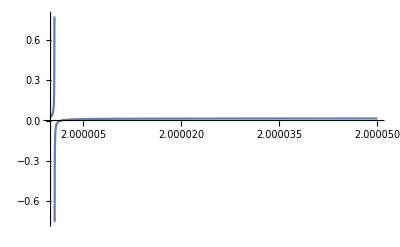

```mathematica
Ints/(16π)//FullSimplify;
%/.{m->1}/.{c1->1.3}/.{c2->0.1}//FullSimplify;
Plot[%,{r,2,2.00005},PlotRange->All]
```

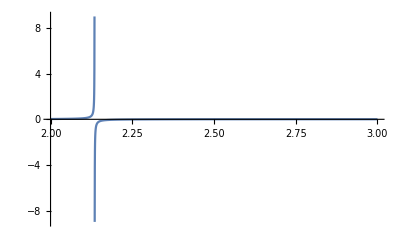

```mathematica
Ints/(16π)//FullSimplify;
%/.{m->1}/.{c1->1}/.{c2->1}//FullSimplify;
Plot[%,{r,2,3},PlotRange->All]
```

##### VANISHING c1

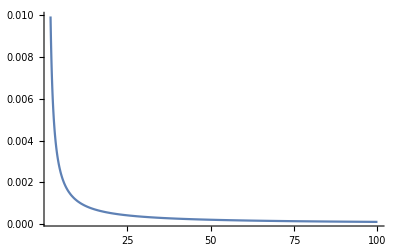

```mathematica
Ints/(16π)//FullSimplify;
%/.{m->1}/.{c1->1}//FullSimplify;
%/.{c2->0};
Plot[%,{r,2,100},PlotRange->Full]
```

#### BROWN-YORK COMPARISON

##### RADIAL MEAN CURV

```mathematica
ExtrinsicLcalcA[r,1,g3s,X3s,X2s,3];
kr=FullSimplify[Tr[gin2s.%],Assumptions->Join[assum,{r>m}]]
```

(2 √(-2 m+r))/r^(3/2)

##### REFERENCE MEAN CURV

```mathematica
ExtrinsicLcalcA[r,1,η3s,X3s,X2s,3];
k0=FullSimplify[Tr[gin2s.%]/.{c1->1,c2->0},Assumptions->Join[assum,{r>2m}]]
```

2/r

##### MEAN CURV DIFFERENCE

```mathematica
diffk=FullSimplify[(kr-k0)√Det[g2s],Assumptions->Join[assum,{r>m}]];
```

##### BROWN-YORK INTEGRAL

```mathematica
IndBY=FullSimplify[-(2π)/(8π)√(-g[[1,1]])∫_0^π diffkⅆθ,Assumptions->Join[assum,{r>m,m>0}]]//FullSimplify
```

2 m-r+√(r (-2 m+r))

```mathematica
Limit[IndBY,r->∞]
```

m

```mathematica
Limit[IndBY,r->2m]
```

0

```mathematica
repsR
```

{r→-m+R}